```mathematica
(*Q0*)
f[x_]:=-5*Sin[Exp[x]] + 5*Cos[Exp[x]] + 5*Sin[Cos[x]]
```

```mathematica
a =D[f[x],{x,3}]
```

-5 (ⅇ^x Cos[ⅇ^x]-ⅇ^(3 x) Cos[ⅇ^x]-3 ⅇ^(2 x) Sin[ⅇ^x])+5 (-3 ⅇ^(2 x) Cos[ⅇ^x]-ⅇ^x Sin[ⅇ^x]+ⅇ^(3 x) Sin[ⅇ^x])+5 (Cos[Cos[x]] Sin[x]+Cos[Cos[x]] Sin[x]^3-3 Cos[x] Sin[x] Sin[Cos[x]])

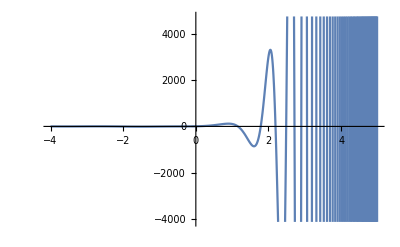

```mathematica
Plot[a,{x,-4,5}]
```

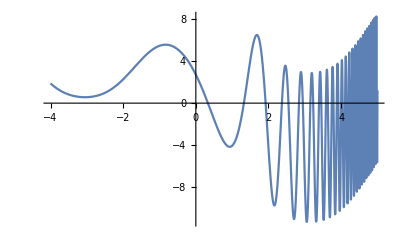

```mathematica
Plot[f[x],{x,-4,5}]
```

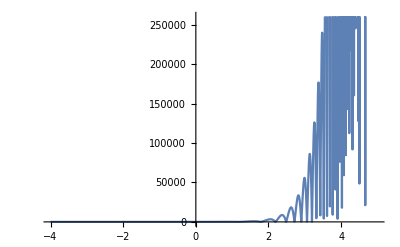

```mathematica
Plot[Abs[a],{x,-4,5}]
```

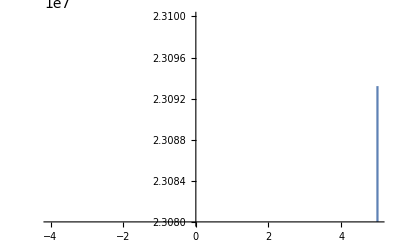

```mathematica
Plot[Abs[f'''[x]],{x,-4,5}, PlotRange->{23080000,23100000}]
```

```mathematica
(*Coordenadas do ponto de máximo e minimo*){{4.991461247901808,2.309332335417282*^7}}
```

```mathematica
FindMaximum[Abs[f'''[x]],x]
```

{119.475,{x→0.897023}}

```mathematica
FindMaximum[Abs[f'''[x]],{x,4.85}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{6.70271×10^6,{x→4.58737}}

```mathematica
(*Formula do erro*)
```

```mathematica
fe = (2.309332335417282*^7)/(3!)*(2.25+4)*(2.25+2)*(2.25-5)
```

-2.81149×10^8

```mathematica
(*Q1*)
```

```mathematica
xi = {-6,1,6};
fi = {1,2,-2};
fixi = Transpose[{xi,fi}];
```

```mathematica
graficoq11 = ListPlot[fixi];
```

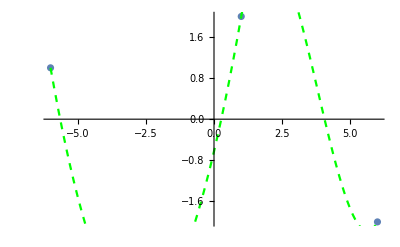

```mathematica
ph1[x_] := 1-(3*(x+6))+(22/49*(x+6)*(x+6))-(2/343*(x+6)*(x+6)*(x-1))
ph2[x_]:= 2+(3*(x-1))-(19/25*(x-1)*(x-1))+(28/125*(x-1)*(x-1)*(x-6))
graficoq12 = Plot[ph1[x],{x,-6,1},PlotRange->{{-6,1},{-10,15}},PlotStyle->{Dashed,Green}];
graficoq13 =Plot[ph2[x],{x,1,6},PlotRange->{{1,6},{-10,15}},PlotStyle->{Dashed,Green}];
Show[{graficoq11, graficoq12, graficoq13}]
```

```mathematica
(*Testando o spline da aula para ver se pode ter inconsistencia nas equações*)
```

```mathematica
xki = {-2,-1,1,2};
fki = {1/5,1/2,1/2,1/5};
fkixki = Transpose[{xki,fki}];
```

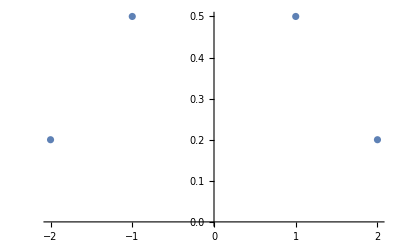

```mathematica
graficok11 = ListPlot[fkixki]
```

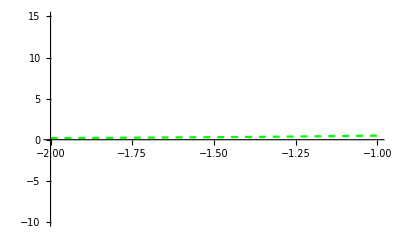

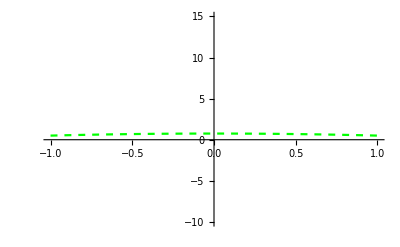

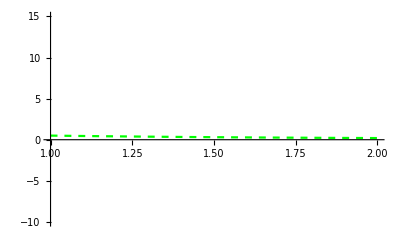

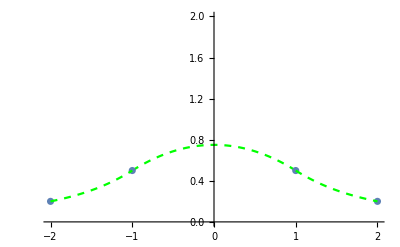

```mathematica
kph1[x_] :=1/5 + 4/25(x+2) + 7/50(x+2)^2 + 3/50(x+2)^2 (x+1)
kph2[x_]:= 1/2 + 1/2(x+1) - 1/4(x+1)^2
kph3[x_]:= 1/2 - 1/2(x-1) + 1/5(x-1)^2 - 3/50(x-1)^2(x-2)
graficok12 = Plot[kph1[x],{x,-2,-1},PlotRange->{{-2,-1},{-10,15}},PlotStyle->{Dashed,Green}]
graficok13 =Plot[kph2[x],{x,-1,1},PlotRange->{{-1,1},{-10,15}},PlotStyle->{Dashed,Green}]
graficok14 =Plot[kph3[x],{x,1,2},PlotRange->{{1,2},{-10,15}},PlotStyle->{Dashed,Green}]
Show[{graficok11, graficok12, graficok13, graficok14},PlotRange->{{-2,2},{0,2}}]
```

```mathematica
(*Q2*)
xpi = {-1,0,1};
fpi = {-1,-2,-3};
fpixpi = Transpose[{xpi,fpi}];
graficop11 = ListPlot[fpixpi];
ps1[x_]:= -1 + d0*(x+1)- (1+d0)*(x+1)^2 + ((d1+d0+2)*x*(x+1)^2) /.{d0-> 0, d1->-9/5}
ps2[x_]:= -2 +(d1*x) - ((1+d1)*x^2) +((d2+d1+2)*x^2*(x-1))/.{d1->-9/5,d2->6/5}

D[ps1[x],{x,0}]
D[ps2[x],{x,0}]
```

-1-(1+x)^2+1/5 x (1+x)^2

-2-(9 x)/5+(4 x^2)/5+7/5 (-1+x) x^2

```mathematica
NSolve[{-2 + 4/5==8/5-2 (1/5+d2) },{d2}]//Rationalize
```

{{d2→6/5}}

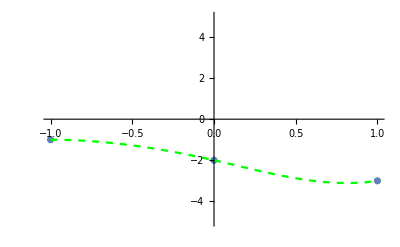

```mathematica
graficop12 = Plot[ps1[x]/.{d0-> 0, d1->-9/5},{x,-1,0},PlotRange->{{-1,0},{-5,5}},PlotStyle->{Dashed,Green}];
graficop13 =Plot[ps2[x]/.{d1->-9/5,d2->6/5},{x,0,1},PlotRange->{{0,1},{-5,0}},PlotStyle->{Dashed,Green}];

Show[{graficop11, graficop12, graficop13},PlotRange->{{-1,1},{-5,5}}]
```